```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh_B

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
numRAD=7;
epsi=1;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["/home/rex/LECs_lambda","Table"]
```

Import::nffil: File /home/rex/LECs_lambda not found during Import.

$Failed

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2 b2+4 lam))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
CalcDimerE[basisW_,lam_,lec_]:=
Module[{eval,evec},
Nd=Length[basisW];
hamm=Table[ham[lam,basisW[[i]],basisW[[j]],lec],{i,Nd},{j,Nd}];
normm=Table[norm[basisW[[i]],basisW[[j]]],{i,Nd},{j,Nd}];
{eval,evec}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];
{eigsorted[[1]],Transpose[{vecsorted[[1]],basisW}]}
];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Print[LECc];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Nd,Ns}];*)

widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-2.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2^(7/2)) (Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2=(π^(3/2)/4) Cc/(lam Bb + Aa(lam + 2Gg +2  Bb) + lam Hh +2 Bb Hh+Gg(lam +2Hh))^(3/2);
w2= 2lam(Aa+Hh)(Gg+Bb)/(lam Bb + Aa(lam+2 Gg+2Bb)+lam Hh +2 Bb Hh+Gg(lam+2Hh));
eta3 =(π^(3/2)/4) Cc/(lam Bb + Gg(lam + 2Bb)+lam Hh +2Bb Hh + Aa(lam+2Gg+2Hh))^(3/2);
w3 = 2lam(Aa+Bb)(Gg+Hh)/(lam Bb + Gg(lam+2Bb)+lam Hh +2Bb Hh+Aa(lam+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq,radMA},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3,Sinh1,Sinh2,Sinh3,CoshA,numRAD=radMA},
zeta1=-(π^(3/2)/(√2))/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

(*SinhA=If[((b1!=0.0)&&(Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Sinh[b1 r rp]/b1,0.0];
SinhB=If[((b2!=0.0)&&(Abs[b2 r rp]<0.1 Abs[a2 r^2+c2 rp^2])&&(Abs[a2 r^2+c2 rp^2]<numRAD)),Exp[-a2 r^2-c2 rp^2] Sinh[b2 r rp]/b2,0.0];
SinhC=If[((b3!=0.0)&&(Abs[b3 r rp]<0.1 Abs[a3 r^2+c3 rp^2])&&(Abs[a3 r^2+c3 rp^2]<numRAD)),Exp[-a3 r^2-c3 rp^2] Sinh[b3 r rp]/b3,0.0];
CoshA=If[((Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Cosh[b1 r rp],0.0];*)
Sinh1=If[b1==0,0,(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1)];
Sinh2=If[b2==0,0,(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2)];
Sinh3=If[b3==0,0,(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3)];

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)

(*SinhA=If[b1==0.0,0.0,(Exp[-a1 r^2-c1 rp^2+b1 r rp]-Exp[-a1 r^2-c1 rp^2-b1 r rp])/(2 b1)];
SinhB=If[b2==0.0,0.0,(Exp[-a2 r^2-c2 rp^2+b2 r rp]-Exp[-a2 r^2-c2 rp^2-b2 r rp])/(2 b2)];
SinhC=If[b3==0.0,0.0,(Exp[-a3 r^2-c3 rp^2+b3 r rp]-Exp[-a3 r^2-c3 rp^2-b3 r rp])/(2 b3)];
CoshA=0.5 (Exp[-a1 r^2-c1 rp^2+b1 r rp]+Exp[-a1 r^2-c1 rp^2+b1 r rp]);*)

(*-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) SinhA-4 a1 Sqrt[3]^-1 (-r rp CoshA+SinhB))+zeta2 SinhB+zeta3 SinhC)*)
(*Chop[Exp[-a3 r^2-c3 rp^2] SinhC,10^-10]*)
]];
(*WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2Pi^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2 Pi^1.5 Cc/(2(2lam+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2 Pi^1.5 Cc/(2(2lam+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam+Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

Sinh1=(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1+100 $MachineEpsilon);
Sinh2=(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2+100 $MachineEpsilon);
Sinh3=(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3+100 $MachineEpsilon);

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];*)
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ,numR_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq,numR],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 

AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001,numR_]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
(*TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
TanDelSwave*){-2.20461,{{-0.00558396,0.050935},{-0.0146543,0.21000},{-0.0406902,0.99319},{-0.691399,6.2469},{0.706724,6.7867},{-0.143551,10.734}}};
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2,numR];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

```mathematica
flag=1;

lambdaTest=6;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
dCores={};
(*WS={4.3584650 ,  2.8802200 ,  2.0651530  , 1.6563710  , 1.1615310  , 0.8261400,0.5922700  , 0.4901080 ,  0.3227900   ,0.2522220  , 0.1357500};
dCores={CalcDimerE[WS,lambdaTest,LECc]}*)

ncc=1;
If[flag>0,
Do[
{eDi,wDi}=ApproxDimerWF[lambdaTest,4,4,10000,0.001,Random[Real,{15,35}],0.01,1,2];
AppendTo[dCores,{eDi,wDi}];
,{nc,Range[ncc]}];
];

If[flag>=0,
NormTF[#]&/@dCores[[All,2]];

dCores=CalcDimerE[dCores[[#]][[2]][[All,2]],lambdaTest,LECc]&/@Range[Length[dCores]];

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#[[2]]]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;

lgd="B(2) = "<>ToString[#[[1]]]&/@dCores;
ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large]
]
```

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==lambdaTest&].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==λ&].

#1⟦1⟧==λ&

λ = 6   C_0(λ) = #1⟦1⟧==λ&  #(width-set candidates) = 39855  in 4 parallel threads.

CompiledFunction::cfsa: Argument #1⟦1⟧==Notebook$$27$935597`λ& at position 4 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

CompiledFunction::cfta: Argument {{-(9.1047+0.00473371 (Equal[«2»]&)-0.00681097 (Times[«2»]+Times[«2»]+Times[«2»]))/(-22.1468-0.000418605 («1»&)+0.00419806 Power[«2»]+0.00419806 Power[«2»])+(1. «1» (-1. (9.1047+Times[«2»]+Times[«2»]) (9.08142+Times[«2»]+Times[«2»])+(-22.1468+«2»+Times[«2»]) «1»))/((-22.1468-0.000418605 («1»&)+0.00419806 Power[«2»]+0.00419806 Power[«2»]) («1»)),19.012},«3»} at position 1 should be a rank 2 tensor of machine-size real numbers.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

CompiledFunction::cfta: Argument {{-(8.06592+0.00638953 (Equal[«2»]&)-0.0100998 (Times[«2»]+Times[«2»]+Times[«2»]))/(-72.4384+0.00104855 («1»&)+0.0137076 Power[«2»]+0.0137076 Power[«2»])+(1. («19»+«1»-«20» («1»)) (-1. Plus[«3»]^2+(«1») («1»)))/((«1») (-1. Plus[«3»] Plus[«3»]+Plus[«4»] Plus[«3»]))+(1. ((«1»)/Plus[«4»]-(«1»)/(«1» «1»)) ((Times[«3»]+Times[«2»]) (Times[«3»]+Times[«2»])-1. (Times[«3»]+Times[«2»]) (Times[«2»]+Times[«2»])))/(Plus[«2»] Plus[«2»]-1. Plus[«2»] Plus[«2»]),«24»},«2»,{1.,«24»}} at position 1 should be a rank 2 tensor of machine-size real numbers.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

CompiledFunction::cfta: Argument {{-(9.25191+0.00482192 (Equal[«2»]&)-0.00697342 (Times[«2»]+Times[«2»]+Times[«2»]))/(-22.0787+0.00175431 («1»&)+0.00404459 Power[«2»]+0.00404459 Power[«2»])+(1. («1») («1»))/((«1») (-1. Plus[«3»] Plus[«3»]+Plus[«4»] Plus[«1»]))+(1. ((«1»)/Plus[«4»]-(«1»)/(«1» «1»)) ((Times[«3»]+Times[«2»]) (Times[«3»]+Times[«2»])-1. (Times[«3»]+Times[«2»]) (Times[«2»]+Times[«2»])))/(Plus[«2»] Plus[«2»]-1. Plus[«2»] Plus[«2»]),19.49},«2»,{1.,23.545}} at position 1 should be a rank 2 tensor of machine-size real numbers.

$Aborted

-Graphics-

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.001;
(* Integration grid *)
rMa=12;
grdPerFermi=15;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
nbrOfCores=Length[dCores];

Do[
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ,numRAD][[1]];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print["core ",nn,"| maxE=",numRAD," )  λ=",lambdaTest," ; C_0(λ)=",LECc," ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; B(2)=",e0Core," ; dim_d=",dimCore," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbar/√(Mm Abs[e0Core]))];
,{nn,Length[dCores]},{numRAD,{1}}];
```

finite-difference runtime Δt = 0.103991 mins     p_match·r_max = 0.0833316

core 1| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=180 ; E_match=0.001 ; B(2)=-2.13551 ; dim_d=4 ; a_dd=2.55143 ; a_dd/a_aa=0.578958

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

20.7369

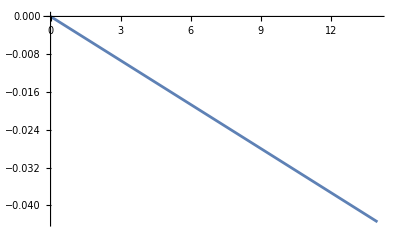

```mathematica
1/mh2
momFM=Sqrt[mh2 0.0002];
Plot[RiccatiBesselJ[momFM r,0]/RiccatiBesselN[momFM r,0](*-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin])*),{r,0,14}]
```

```mathematica
lambdaTest=8;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]]
```

-974.604

Set::write: Tag Dot in Null.7 is Protected.

finite-difference runtime Δt = 0.219748 mins     p_match·r_max = 0.104164

core 1| maxE=7 )  λ = 8   C_0(λ) = -974.604     R_max = 15.     #(grid points) = 180                a_dd = 3.03322 fm        a_dd/a_aa = 0.684006

finite-difference runtime Δt = 0.262008 mins     p_match·r_max = 0.107637

core 1| maxE=7 )  λ = 8   C_0(λ) = -974.604     R_max = 15.5     #(grid points) = 186                a_dd = 3.03322 fm        a_dd/a_aa = 0.684006

finite-difference runtime Δt = 0.272968 mins     p_match·r_max = 0.111109

core 1| maxE=7 )  λ = 8   C_0(λ) = -974.604     R_max = 16.     #(grid points) = 192                a_dd = 3.03322 fm        a_dd/a_aa = 0.684006

finite-difference runtime Δt = 0.298776 mins     p_match·r_max = 0.114581

core 1| maxE=7 )  λ = 8   C_0(λ) = -974.604     R_max = 16.5     #(grid points) = 198                a_dd = 3.03322 fm        a_dd/a_aa = 0.684006

finite-difference runtime Δt = 0.310392 mins     p_match·r_max = 0.118053

core 1| maxE=7 )  λ = 8   C_0(λ) = -974.604     R_max = 17.     #(grid points) = 204                a_dd = 3.03322 fm        a_dd/a_aa = 0.684006

finite-difference runtime Δt = 0.324531 mins     p_match·r_max = 0.121525

core 1| maxE=7 )  λ = 8   C_0(λ) = -974.604     R_max = 17.5     #(grid points) = 210                a_dd = 3.03322 fm        a_dd/a_aa = 0.684006

finite-difference runtime Δt = 0.345894 mins     p_match·r_max = 0.124997

core 1| maxE=7 )  λ = 8   C_0(λ) = -974.604     R_max = 18.     #(grid points) = 216                a_dd = 3.03322 fm        a_dd/a_aa = 0.684006

finite-difference runtime Δt = 0.372161 mins     p_match·r_max = 0.12847

core 1| maxE=7 )  λ = 8   C_0(λ) = -974.604     R_max = 18.5     #(grid points) = 222                a_dd = 3.03322 fm        a_dd/a_aa = 0.684006

$Aborted

Transpose::nmtx: The first two levels of {{15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,«1»},{3.03322,3.03322,3.03322,3.03322,3.03322,3.03322,3.03322,3.03322}} cannot be transposed.

ListPlot::lpn: Transpose[{{15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,«1»},{3.03322,3.03322,3.03322,3.03322,3.03322,3.03322,3.03322,3.03322}}] is not a list of numbers or pairs of numbers.

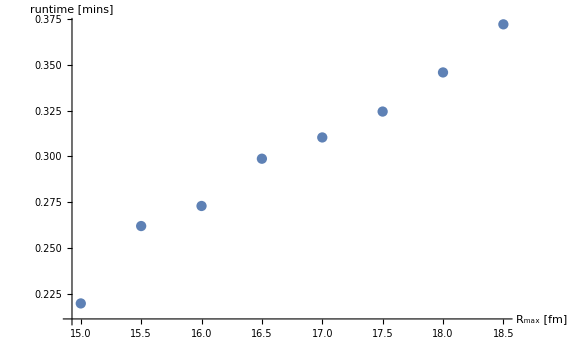
ListPlot[Transpose[{{15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.},{3.03322,3.03322,3.03322,3.03322,3.03322,3.03322,3.03322,3.03322}}],ImageSize→Large,Joined→True,AxesLabel→{R_max [fm],a_dd [fm]}] | -Graphics-

```mathematica
rMaxStart=15;
rMaxEnd=20;
nbrR=10;
coreNBR=1;
{e0Core,dimerCore}={-2.1090463086254503,{{-0.10584211573369443,0.0865450191017237578`5.},{-0.3023667802347377,0.6253090465278050692`5.},{-0.29582447283399416,2.8046877609185618441`5.},{-0.3898779087148401,4.2015875044423103259`5.},{-0.8110825323702425,14.0649537134389835903`5.}}};
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=12;.
numRAD=9;
results={};
resultsWF={};
runtimes={};
NormTF[dimerCore]
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ,numRAD];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,tmp2];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["core ",coreNBR,"| maxE=",numRAD," )  λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

```mathematica
0.10259664914435505
```

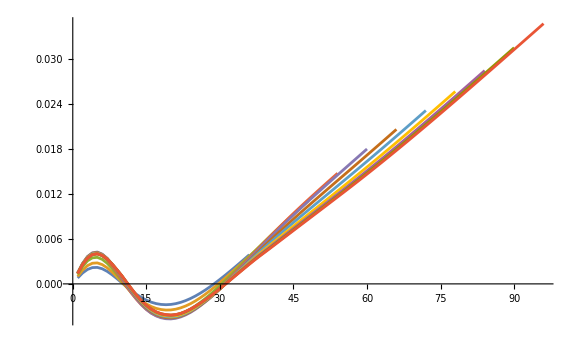

```mathematica
ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large]
```